## dσ/dY

```mathematica
(*                                         -Graphics-                                 *)
```

```mathematica
Clear["Global`*"]
```

Photon spectrum for Proton 1 (Elastic)

```mathematica
α=1/137;
mp=0.938;  (* Mass of proton in GeV *)
Ep= 7000;   (* Energy of proton beam in GeV *)


GE2[q2_]:=(1+q2/0.71)^{-4}; 
GM2[q2_]:=7.78*GE2[q2]; 

FE[q2_]:=(4  mp^2  GE2[q2]+ q2  GM2[q2])/(4 mp^2 + q2);  (* Electric Form Factor *)
FM[q2_]:=GM2[q2];                                                                                     (* Magnetic Form Factor *)

Plot[FE[q2],{q2,1,1000},Frame->True];
Plot[FM[q2],{q2,1,1000},Frame->True];

q2minp[yp1_]:=(mp^2  yp1^2)/(1-yp1);   (* For the case of elastic *)
q2maxp = 100000;
```

```mathematica
PhotonFluxProton1[yp1_,prec_:MachinePrecision]:=1/yp1*α/π*NIntegrate[((1-yp1)(1-q2minp[yp1]/q2)*FE[q2] +  yp1^2/2 *FM[q2]) 1/q2 ,{q2,q2minp[yp1],q2maxp}, MaxRecursion -> 100(*,PrecisionGoal->12,AccuracyGoal->15,WorkingPrecision->10*)];  (* //Simplify *)
```

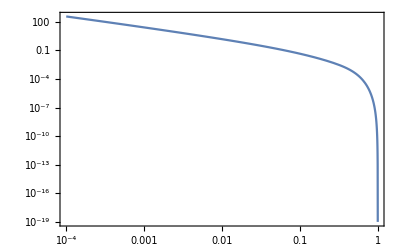

```mathematica
LogLogPlot[PhotonFluxProton1[yp1],{yp1,0.0001,0.9999},PlotRange->Full,Frame->True]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

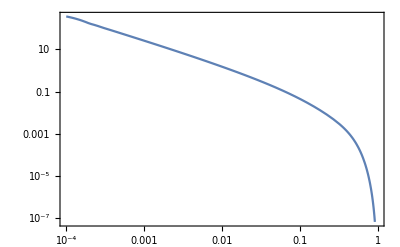

```mathematica
PhotonFluxProtonList1=ParallelTable[Flatten[{yp1, PhotonFluxProton1[yp1]}],{yp1,0.0001,0.9999,0.0001}];
funPhotonFluxProtonList1=Interpolation[PhotonFluxProtonList1]
PhotonFluxProtonFinal1=FunctionInterpolation[funPhotonFluxProtonList1[yp1],{yp1,0.0001,0.9999}]
LogLogPlot[PhotonFluxProtonFinal1[yp1],{yp1,0.0001,0.9999},Frame->True]
```

Photon spectrum for Proton 2 (Elastic)

```mathematica
α=1/137;
mp=0.938;  (* Mass of proton in GeV *)
Ep= 7000;   (* Energy of proton beam in GeV *)


GE2[q2_]:=(1+q2/0.71)^{-4}; 
GM2[q2_]:=7.78*GE2[q2]; 

FE[q2_]:=(4  mp^2  GE2[q2]+ q2  GM2[q2])/(4 mp^2 + q2);  (* Electric Form Factor *)
FM[q2_]:=GM2[q2];                                                                                     (* Magnetic Form Factor *)

Plot[FE[q2],{q2,1,1000},Frame->True];
Plot[FM[q2],{q2,1,1000},Frame->True];

q2minp[yp2_]:=(mp^2  yp2^2)/(1-yp2);   (* For the case of elastic *)
q2maxp = 100000;
```

```mathematica
PhotonFluxProton2[yp2_,prec_:MachinePrecision]:=1/yp2*α/π*NIntegrate[((1-yp2)(1-q2minp[yp2]/q2)*FE[q2] +  yp2^2/2 *FM[q2]) 1/q2 ,{q2,q2minp[yp2],q2maxp}, MaxRecursion -> 100(*,PrecisionGoal->12,AccuracyGoal->15,WorkingPrecision->10*)];  (* //Simplify *)
```

```mathematica
LogLogPlot[PhotonFluxProton2[yp2],{yp2,0.0001,0.9999},PlotRange->Full,Frame->True]
```

-Graphics-

```mathematica
PhotonFluxProtonList2=ParallelTable[Flatten[{yp2, PhotonFluxProton2[yp2]}],{yp2,0.0001,0.9999,0.0001}];
funPhotonFluxProtonList2=Interpolation[PhotonFluxProtonList2]
PhotonFluxProtonFinal2=FunctionInterpolation[funPhotonFluxProtonList2[yp2],{yp2,0.0001,0.9999}]
LogLogPlot[PhotonFluxProtonFinal2[yp2],{yp2,0.0001,0.9999},Frame->True]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

-Graphics-

```mathematica
csbbbar[wvalue_]:=Module[{mbquark,chargbqaurk,hbarc2,alpha2,beta,cs},

mbquark=4.5;
chargbqaurk = 1.0/3.0;
Nc =3.0;

hbarc2=0.389;
alpha2=(1.0/137.0)*(1.0/137.0);

(*Element-wise calculation of beta using If*)
beta=Sqrt[If[1.0-4.0*mbquark*mbquark/wvalue^2.0>=0,1.0-4.0*mbquark*mbquark/wvalue^2.0,Indeterminate]];

(*Element-wise calculation of cs using If*)

cs=If[wvalue>mbquark,chargbqaurk^4.0 * Nc*(4.0*π*alpha2*hbarc2)/wvalue^2.0*(beta)*((3.0-(beta^4.0))/(2.0*beta)*Log[(1.0+beta)/(1.0-beta)]-2.0+beta^2.0),0.]*10^9;
cs]

(*Example usage:*)
wvalue=125.0000001;
result=csbbbar[wvalue]
```

3.50513

```mathematica
Ep1 = 7000;
Ep2 = 7000;
Sqrts=(4.0 * Ep1 * Ep2)^0.5;                                  (* Center of mass energy in GeV *)

yp1[W_,Y_]:=W ⅇ^-Y/(2 Ep1);
yp2[W_,Y_]:=W ⅇ^Y/(2 Ep2);
```

```mathematica
Flux[W_,Y_]:=Re[PhotonFluxProtonFinal1[yp1[W,Y]]*PhotonFluxProtonFinal2[yp2[W,Y]]*Boole[0.0<=yp1[W,Y]<=1.0]*Boole[0.0<=yp2[W,Y]<=1.0]];
```

```mathematica
dSigmadY=ParallelTable[Flatten[{Y,2.0/Sqrts^2.0*NIntegrate[csbbbar[W]* W * Flux[W,Y],{W,125.0000001,Sqrts},MaxRecursion->100]}],{Y,-3.5,+3.5,0.01}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

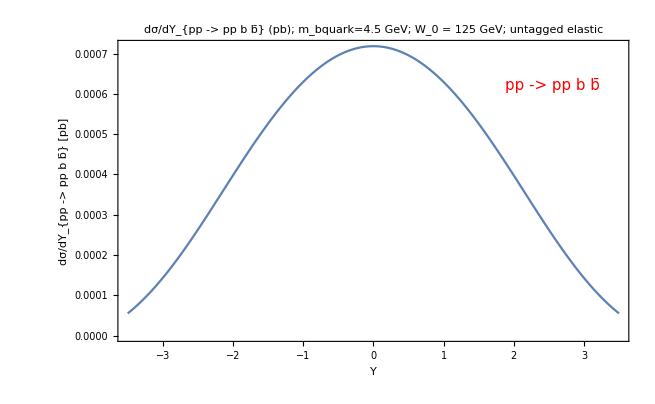

```mathematica
ListPlot[dSigmadY,PlotRange->All,PlotLabel->TraditionalForm["dσ/dY_{pp -> pp b b̄} (pb); m_bquark=4.5 GeV; W_0 = 125 GeV; untagged elastic"],FrameLabel->{"Y","dσ/dY_{pp -> pp b b̄} [pb]"},Frame->True,Joined->True,Epilog->{Text[Style["pp -> pp b b̄",FontSize->15,Red],Scaled[{0.85,0.85}]]}]
```

```mathematica
Export["C:\\Users\\Hamzeh\\Dropbox\\Photon_Photon_Interaction_LHC_LHeC\\dSigmadY\\dSigmadY_pp_bbbar_New.pdf",%]
```

C:\Users\Hamzeh\Dropbox\Photon_Photon_Interaction_LHC_LHeC\dSigmadY\dSigmadY_pp_bbbar_New.pdf

C:\Users\Hamzeh\Dropbox\Photon_Photon_Interaction_LHC_LHeC\dSigmadY\dSigmadY_pp_bbbar_New.pdf

C:\Users\Hamzeh\Dropbox\Photon_Photon_Interaction_LHC_LHeC\dSigmadY\dSigmadY_pp_bbbar_New.pdf